```mathematica
Clear All



Subscript[g, 1][n_]:=Sqrt[n];

Subscript[g, 2][m_]:=Sqrt[m];
s=√10;
r=√10;

l=50;
```

All Clear

```mathematica
Θ[τ_,p1_,p2_]:= τ/2 Cos[τ*(p1-p2)]-1/(4*p1)Sin[2*p1*τ];
Subscript[q, 1][n_]:=Exp[-Abs[s]^2/2]*s^n/(√(n!));
Subscript[q, 2][m_]:=Exp[-Abs[r]^2/2]*r^m/(√(m!));
```

```mathematica
f1[m_,n_]:=Subscript[g, 1][n+1]*Subscript[g, 2][m+1]*Sqrt[(n+1)*(m+1)];
f2[m_,n_]:=Subscript[g, 1][n+2]*Subscript[g, 2][m+2]*Sqrt[(n+2)*(m+2)];
f[m_,n_]:=Sqrt[f1[m,n]^2+f2[m,n]^2];
```

```mathematica
A[m_,n_,τ_,p1_,p2_]:=f1[m,n]^2/f[m,n]^2*Cos[2*Θ[τ,p1,p2]*f[m,n]]+f2[m,n]^2/f[m,n]^2;
```

```mathematica
B[m_,n_,τ_,p1_,p2_]:=-(I*f1[m,n])/(2*f[m,n])*Sin[2*Θ[τ,p1,p2]*f[m,n]];
```

```mathematica
Dm[m_,n_,τ_,p1_,p2_]:=-(I*f1[m,n])/(2*f[m,n])*Sin[2*Θ[τ,p1,p2]*f[m,n]];
```

```mathematica
Fm[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
k[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
NN[m_,n_,τ_,p1_,p2_]:=(f1[m,n]*f2[m,n])/(2*f[m,n]^2)*(Cos[2*Θ[τ,p1,p2]*f[m,n]^2]-1);
```

```mathematica
nf[τ_,p1_,p2_]:=(∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*(Abs[A[m,n,τ,p1,p2]]^2+2*Abs[B[m,n,τ,p1,p2]]^2+2*Abs[Dm[m,n,τ,p1,p2]]^2+Abs[Fm[m,n,τ,p1,p2]]^2+2*Abs[k[m,n,τ,p1,p2]]^2+Abs[NN[m,n,τ,p1,p2]]^2))^(-1);
```

```mathematica
Subscript[ρ, 11][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[A[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[ρ, 22][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[B[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[ρ, 44][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[Dm[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[ρ, 12][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*A[m+1,n+1,τ,p1,p2]*Conjugate[B[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 16][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+2]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+2]*Conjugate[Subscript[q, 2][m]]*A[m+2,n+2,τ,p1,p2]*Conjugate[Fm[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 26][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*A[m+1,n+1,τ,p1,p2]*Conjugate[B[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 47][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*Dm[m+1,n+1,τ,p1,p2]*Conjugate[k[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 14][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*A[m+1,n+1,τ,p1,p2]*Conjugate[Dm[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 27][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*B[m+1,n+1,τ,p1,p2]*Conjugate[k[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 49][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Subscript[q, 1][n+1]*Conjugate[Subscript[q, 1][n]]*Subscript[q, 2][m+1]*Conjugate[Subscript[q, 2][m]]*Dm[m+1,n+1,τ,p1,p2]*Conjugate[NN[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 66][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[Fm[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[ρ, 77][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[k[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[ρ, 24][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*B[m,n,τ,p1,p2]*Conjugate[Dm[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 67][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Fm[m,n,τ,p1,p2]*Conjugate[k[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 79][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*k[m,n,τ,p1,p2]*Conjugate[NN[m,n,τ,p1,p2]];
```

```mathematica
Subscript[ρ, 99][τ_,p1_,p2_]:=nf[τ,p1,p2]*∑_(n=0)^l ∑_(m=0)^l Abs[Subscript[q, 1][n]]^2*Abs[Subscript[q, 2][m]]^2*Abs[NN[m,n,τ,p1,p2]]^2;
```

```mathematica
Subscript[α, 11][τ_,p1_,p2_]:=Module[{p11,p22,p44},p11= Subscript[ρ, 11][τ,p1,p2];p22=Subscript[ρ, 22][τ,p1,p2];p44=Subscript[ρ, 44][τ,p1,p2];p11+p22+p44];
```

```mathematica
Subscript[α, 12][τ_,p1_,p2_]:=Module[{p12,p16,p26,p47},p12= Subscript[ρ, 12][τ,p1,p2];p16=Subscript[ρ, 16][τ,p1,p2];p26=Subscript[ρ, 26][τ,p1,p2];p47=Subscript[ρ, 47][τ,p1,p2];p12+p16+2*p26+p47];
```

```mathematica
Subscript[α, 13][τ_,p1_,p2_]:=Module[{p14,p27,p49},p14= Subscript[ρ, 14][τ,p1,p2];p27=Subscript[ρ, 27][τ,p1,p2];p49=Subscript[ρ, 49][τ,p1,p2];p14+p27+p49];
```

```mathematica
Subscript[α, 21][τ_,p1_,p2_]:=Module[{p12,p26,p47},p12= Conjugate[Subscript[ρ, 12][τ,p1,p2]];p26=Conjugate[Subscript[ρ, 26][τ,p1,p2]];p47=Conjugate[Subscript[ρ, 47][τ,p1,p2]];p12+p26+p47];
```

```mathematica
Subscript[α, 22][τ_,p1_,p2_]:=Module[{p22,p66,p77},p22= Subscript[ρ, 22][τ,p1,p2];p66=Subscript[ρ, 66][τ,p1,p2];p77=Subscript[ρ, 77][τ,p1,p2];p22+p66+p77];
```

```mathematica
Subscript[α, 23][τ_,p1_,p2_]:=Module[{p24,p67,p79},p24= Subscript[ρ, 24][τ,p1,p2];p67=Subscript[ρ, 67][τ,p1,p2];p79=Subscript[ρ, 79][τ,p1,p2];p24+p67+p79];
```

```mathematica
Subscript[α, 31][τ_,p1_,p2_]:=Module[{p41,p72,p94},p41=Conjugate[ Subscript[ρ, 14][τ,p1,p2]];p72=Conjugate[Subscript[ρ, 27][τ,p1,p2]];p94=Conjugate[Subscript[ρ, 49][τ,p1,p2]];p41+p72+p94];
```

```mathematica
Subscript[α, 32][τ_,p1_,p2_]:=Module[{p42,p76,p97},p42=Conjugate[ Subscript[ρ, 24][τ,p1,p2]];p76=Conjugate[Subscript[ρ, 67][τ,p1,p2]];p97=Conjugate[Subscript[ρ, 79][τ,p1,p2]];p42+p76+p97];
```

```mathematica
Subscript[α, 33][τ_,p1_,p2_]:=Module[{p44,p77,p99},p44= Subscript[ρ, 44][τ,p1,p2];p77=Subscript[ρ, 77][τ,p1,p2];p99=Subscript[ρ, 99][τ,p1,p2];p44+p77+p99];
```

```mathematica
Ent[τ_,p1_,p2_] :=Module[{a11,a12,a13,a21,a22,a23,a31,a32,a33},a11=Subscript[α, 11][τ,p1,p2];a12=Subscript[α, 12][τ,p1,p2];a13=Subscript[α, 13][τ,p1,p2];a21=Subscript[α, 21][τ,p1,p2];a22=Subscript[α, 22][τ,p1,p2];a23=Subscript[α, 23][τ,p1,p2];a31=Subscript[α, 31][τ,p1,p2];a32=Subscript[α, 32][τ,p1,p2];a33=Subscript[α, 33][τ,p1,p2];Sqrt[2-2*(a11^2+2*a12*a21+2*a13*a31+a22^2+2*a23*a32+a33^2)]];
```

```mathematica
a=Re[Ent[τ,2,2]];
b=Re[Ent[τ,4,4]];
c=Re[Ent[τ,6,6]];
```

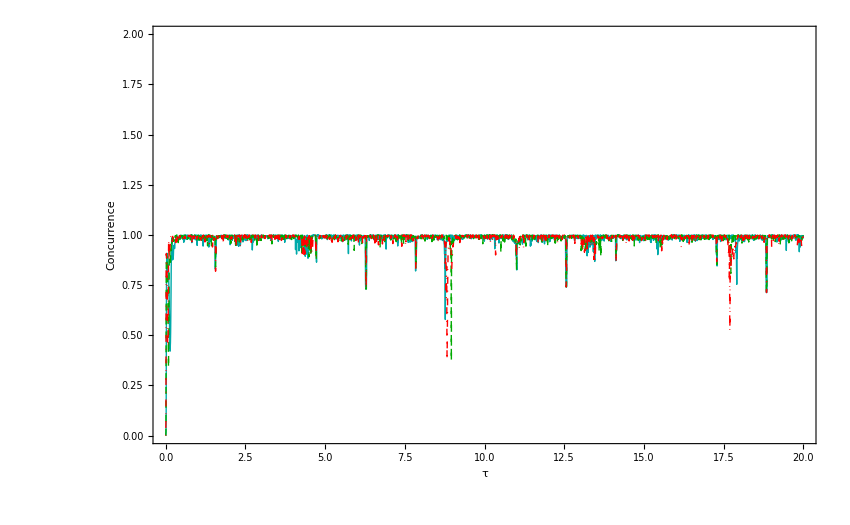

```mathematica
multient=Plot[{a,b,c},{τ,0,20},PlotRange->{{0,20},{0,2}},Frame->True,FrameLabel->{τ,"Concurrence  "},RotateLabel->True,PlotStyle->{{Darker[Cyan]},{Darker[Green],Dashed},{Red,DotDashed}},ImageSize->850,LabelStyle->Directive[Green,35],FrameStyle->Directive[Blue,AbsoluteThickness[4]]]
```

```mathematica
Show[multient,PlotRange->{{0,20},{0,1.2}}]
```

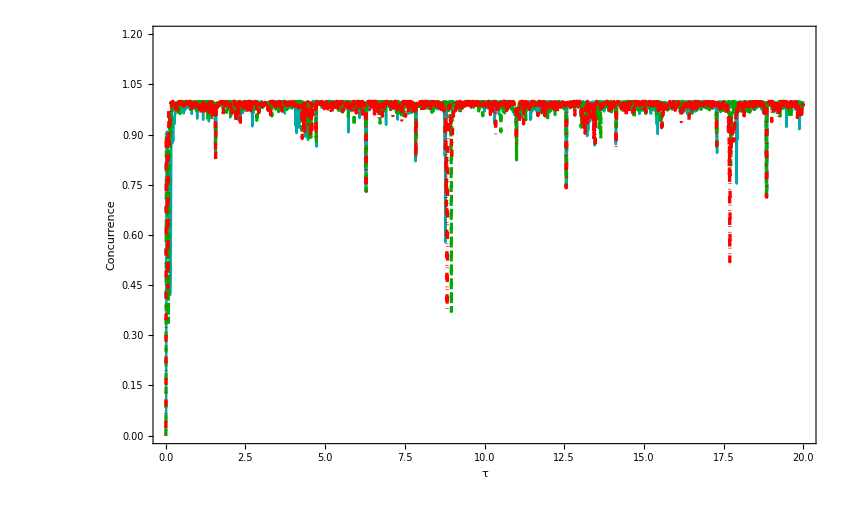

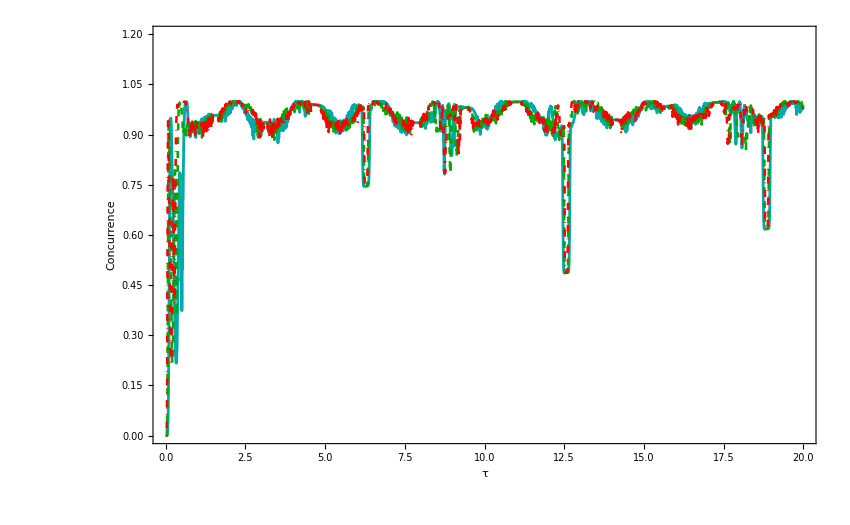

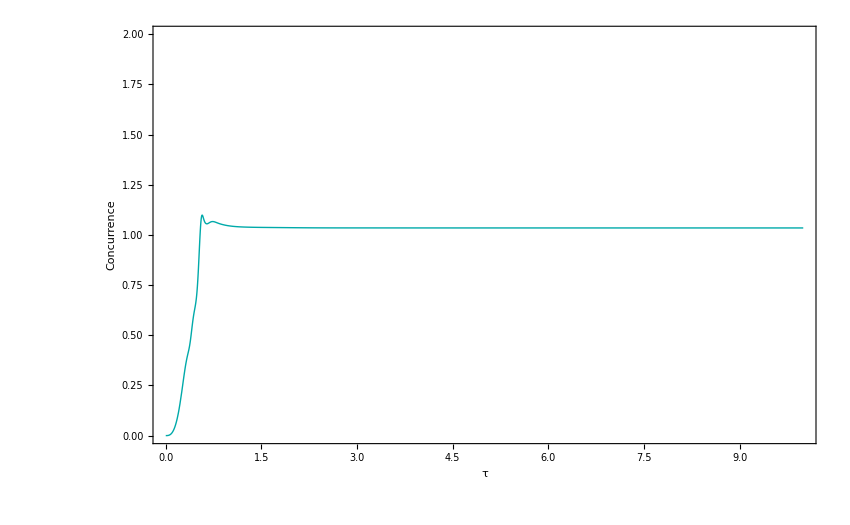
```mathematica
-Graphics-
Show[multient,PlotRange->{{0,10},{0,1.2}}]
```

-Graphics-

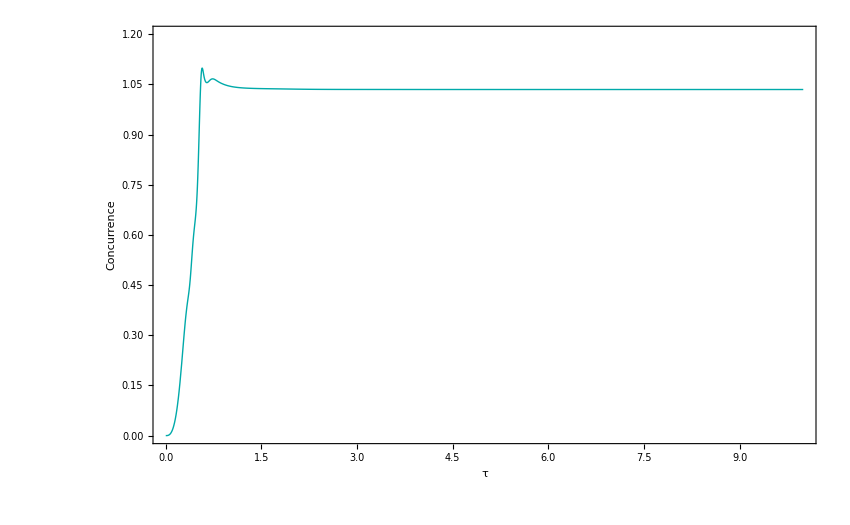

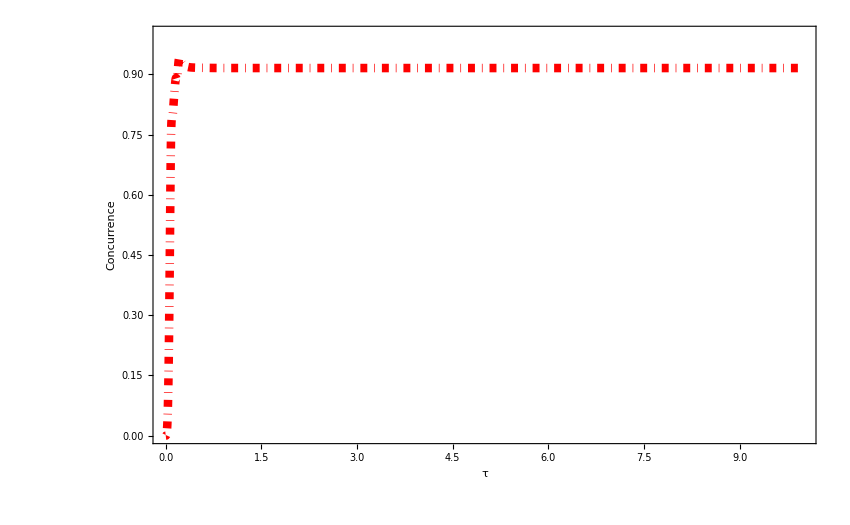

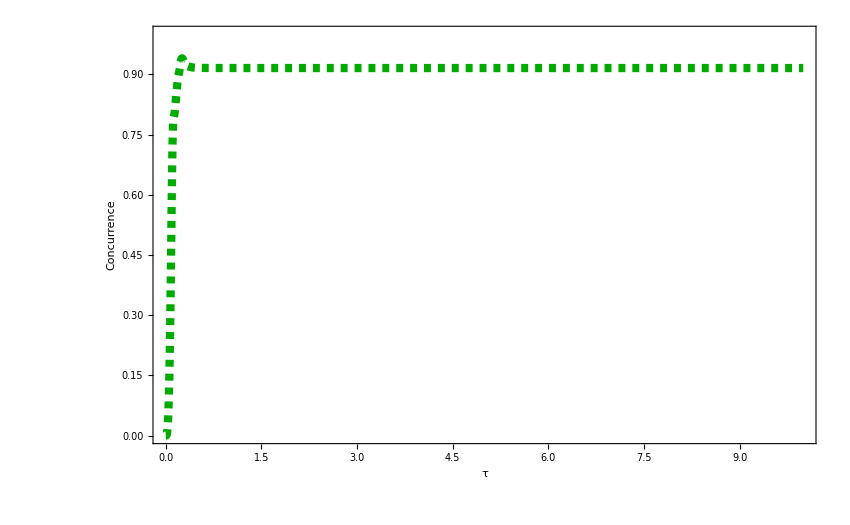

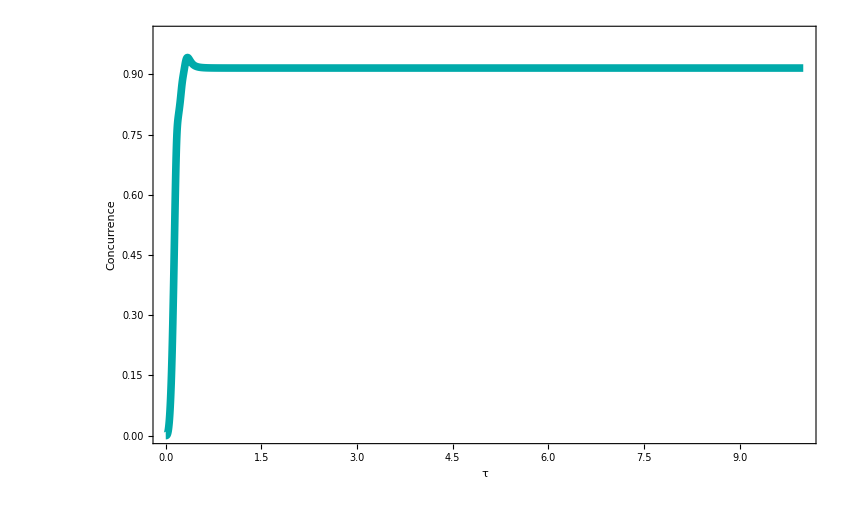

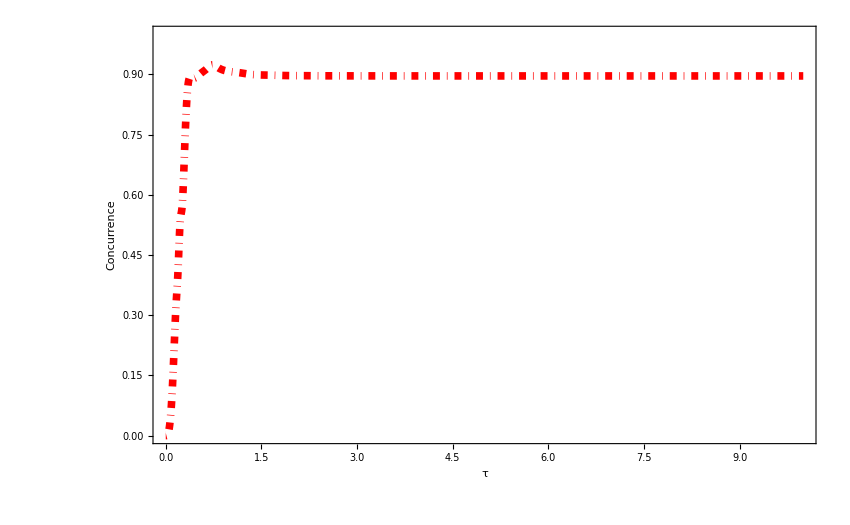

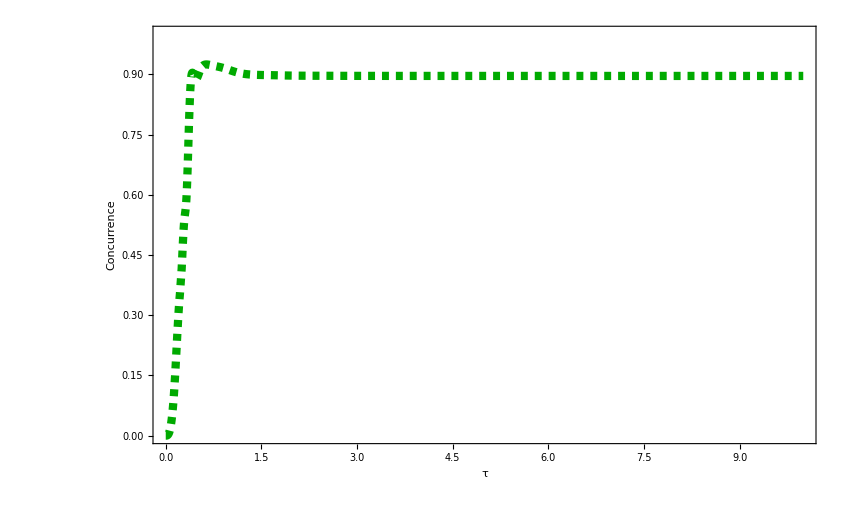

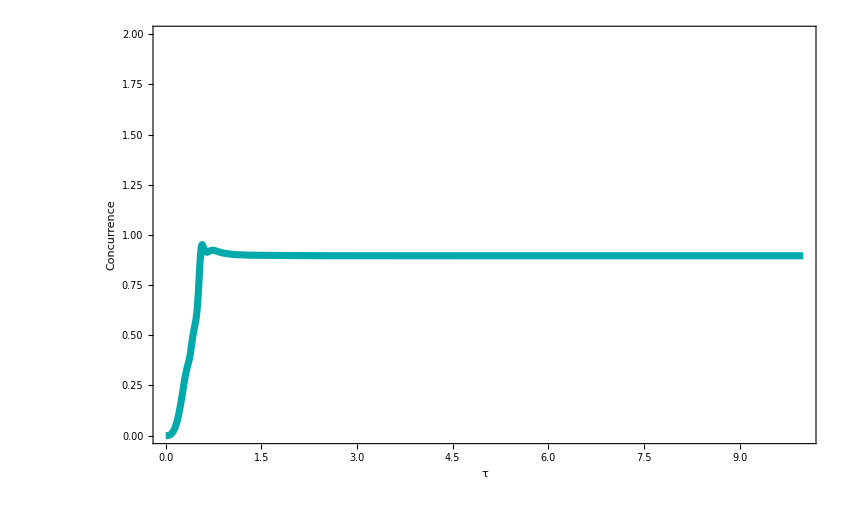

```mathematica
Show[multient,PlotRange->{{0,10},{0,1}}]
```